```mathematica
(*
consulta = "df = pd.read_sql(\"\"\"SELECT patient_id,frace,document_id,token_cancer from Alltokens where document_id 
    between 0 and 1000 and token_cancer in ('CANCER_CONCEPT', 'COMORBIDITY', 'AGE', 'TNM', 'TREATMENT_NAME','DRUG','SURGERY')
    group by document_id,patient_id,frace,token_cancer \"\"\" , con)
    print(df.head(10))
    df.to_csv('alltokens.csv', index=False) ";
*)
```

```mathematica
data=Import["C:\\Users\\brian\\Documents\\00-SEMESTRE-2003-II\\Sistemas complejos\\Proyecto\\alltokens.csv", "Data"];
size = Length[data];
```

Text Normalization

```mathematica
Table[If[StringQ[data[[i,2]]],data[[i,2]]=RemoveDiacritics[ToLowerCase[data[[i,2]]]]],{i,Length[data]}];
```

```mathematica
(*Vista del dataset*)
Table[data[[i,j]],{i,Length[data]},{j,Length[data[[1]]]}] //TableView;
```

```mathematica
RemoveDiacritics["cáncer de mama carcinóma"]
```

cancer de mama carcinoma

Número de registros considerados:

```mathematica
numRegToEval = size-1;
```

ReAjuste de términos sobre dataset para facilitar la visualización del grafo

```mathematica
reglasTokens = {
"AGE"-> "Ag",
"CANCER_CONCEPT" -> "CC",
"COMORBIDITY"-> "Cm",
"DRUG" -> "Dg",
"SURGERY"-> "Sg",
"TNM"-> "TNM",
"TREATMENT_NAME"-> "TN"
};
```

```mathematica
dataFixed = data;
```

```mathematica
dataFixed // TableView;
```

```mathematica
(*Cambio sobre los tokens para su visualizacion*)
dataFixed = dataFixed /. reglasTokens;
(*Cambio registros pacientes - prefijo P*)
Table[dataFixed[[i,1]]= "P:"<>ToString[dataFixed[[i,1]]],{i, 2,numRegToEval}];
(*Cambio registros #doc historia - prefijo H*)
Table[dataFixed[[i,3]]= "H:"<>ToString[dataFixed[[i,3]]],{i, 2,numRegToEval}];
```

```mathematica
EdgeStyling[i_,data_]:= 
Switch[data[[i,4]],
"Ag",Style[data[[i,2]]<-> data[[i,3]],Green],
"CC",Style[data[[i,2]]<-> data[[i,3]],Blue],
"Cm",Style[data[[i,2]]<-> data[[i,3]],Yellow],
"Dg",Style[data[[i,2]]<-> data[[i,3]],Red],
"Sg",Style[data[[i,2]]<-> data[[i,3]],Orange],
"TNM",Style[data[[i,2]]<-> data[[i,3]], Purple],
"TN",Style[data[[i,2]]<-> data[[i,3]], Magenta]];
```

PRUEBA CAMBIO EDGE STYLING  definicion de diccionario con los nodos de cada tipo de token

```mathematica
dicTokens=<|"Ag"->{},"CC"->{},"Cm"->{},"Dg"->{},"Sg"->{},"TNM"->{},"TN"->{}|>;
```

```mathematica
EdgeStyling[i_,data_]:= Module[{},
AppendTo[dicTokens[data[[i,4]]],data[[i,2]]];
Switch[data[[i,4]],
"Ag",Style[data[[i,2]]<-> data[[i,3]],Green],
"CC",Style[data[[i,2]]<-> data[[i,3]],Blue],
"Cm",Style[data[[i,2]]<-> data[[i,3]],Yellow],
"Dg",Style[data[[i,2]]<-> data[[i,3]],Red],
"Sg",Style[data[[i,2]]<-> data[[i,3]],Orange],
"TNM",Style[data[[i,2]]<-> data[[i,3]], Purple],
"TN",Style[data[[i,2]]<-> data[[i,3]], Magenta]]
];
```

```mathematica
nodos = {};
GenerateGraph[data_]:= Module[{doc},
doc = data[[2,3]];
AppendTo[nodos,Labeled[data[[2,1]]<->data[[2,3]],"patient"]];
For[i=2,i<numRegToEval,i++,
AppendTo[nodos,Labeled[EdgeStyling[i,data],data[[i,4]]]];
If[doc != data[[i,3]],AppendTo[nodos,Labeled[data[[i,1]]<->data[[i,3]],"patient"]]; doc=data[[i,3]]];]]

GenerateGraph[dataFixed];
initialGraph = Graph[nodos];
(*SimpleGraph[gp]*)
```

Ajuste de diccionario de nodos en el grafo

```mathematica
dicTokens=AssociationThread[Keys[dicTokens]->Map[DeleteDuplicates,Values[dicTokens]]];
```

Definición del tamaño de los nodos según su grado y arreglo de visualización del grafo

```mathematica
VertexSizes[graph_]:=Module[{sizesVertex={}},
grados=VertexDegree[graph];
vertexs= VertexList[graph];
Table[AppendTo[sizesVertex,If[StringContainsQ[vertexs[[i]],"P:"|"H:"],vertexs[[i]]->1,vertexs[[i]]->1+0.1grados[[i]]]],{i,1,VertexCount[graph]}];
sizesVertex
];
```

```mathematica
shownGraph=Graph[ nodos, VertexLabels->Placed[Automatic,Center], VertexSize->VertexSizes[initialGraph], GraphLayout->"GravityEmbedding"];
```

StringContainsQ::strse: String or list of strings expected at position 1 in StringContainsQ[197,P:|H:].

StringContainsQ::strse: String or list of strings expected at position 1 in StringContainsQ[67,P:|H:].

StringContainsQ::strse: String or list of strings expected at position 1 in StringContainsQ[88,P:|H:].

General::stop: Further output of StringContainsQ::strse will be suppressed during this calculation.

Parte pendiente de revisar ---------

```mathematica
(*Seccion que busca sacar la que sería la lista de nodos particular en una columna, en este caso documentos, con el fin de poderles darles estilo de manera individual*)
documentos = {};
Table[AppendTo[documentos,dataFixed[[i,3]]],{i,2, numRegToEval}];
Table[dataFixed[[i,1]],{i, 2,numRegToEval}];
documentos=DeleteDuplicates[documentos];
```

```mathematica
(*Resaltando nodos de tokens*)
shownGraph=HighlightGraph[shownGraph,Style[dicTokens["Ag"],LightGreen]];
shownGraph =HighlightGraph[shownGraph,Style[dicTokens["CC"],LightBlue]];
shownGraph=HighlightGraph[shownGraph,Style[dicTokens["Cm"],LightYellow]];
shownGraph=HighlightGraph[shownGraph,Style[dicTokens["Dg"],LightRed]];
shownGraph=HighlightGraph[shownGraph,Style[dicTokens["Sg"],LightOrange]];
shownGraph=HighlightGraph[shownGraph,Style[dicTokens["TNM"],LightPurple]];
shownGraph=HighlightGraph[shownGraph,Style[dicTokens["TN"],LightMagenta]];
(*shownGraph = HighlightGraph[shownGraph, documentos, GraphHighlightStyle -> "VertexConcaveDiamond"];*)
```

```mathematica
CommunityGraphPlot[shownGraph, PlotLegends->Placed[Automatic,Below]];
```

Revisión de comunidades, análisis que busca segmentar grupos de pacientes

```mathematica
comunidades=FindGraphCommunities[shownGraph];
comunidadesPacientes ={};
If[Length[comunidades]>=1,
Table[AppendTo[comunidadesPacientes,Select[comunidades[[i]],StringMatchQ[#,"P:"~~NumberString]&]],{i,1,Length[comunidades]}]
];
comunidadesPacientes;
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[197,P:~~NumberString].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[67,P:~~NumberString].

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[58,P:~~NumberString].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

Selección de comunidades que tienen mayor representación sobre todo el dataset para su posterior comparación

```mathematica
selectedCommunities={};
Module[{sizeComunidades={},representativiyComty={}},
Table[AppendTo[sizeComunidades,Length[comunidadesPacientes[[i]]]],{i,1,Length[comunidadesPacientes]}];
totalPacientes=Total[sizeComunidades];
(*Calcular respresentatividad por comunidad*)

Table[AppendTo[representativiyComty,sizeComunidades[[i]]/totalPacientes],{i,1 ,Length[comunidadesPacientes]}];
(*Umbral valido para ser aceptado*)
umbralRepresentativity = 0.05;
Table[If[representativiyComty[[i]]>=umbralRepresentativity,AppendTo[selectedCommunities,comunidadesPacientes[[i]]]],{i,1,Length[comunidadesPacientes]}];
N[representativiyComty];
]
Length[selectedCommunities]
```

4

A partir de las comunidades seleccionadas que superan el umbral de representación definido, se selecciona dos nodos de participantes  por comunidad, los cuales tengan el mayor número de enlaces.

```mathematica
vertexDegreeL=Table[Map[VertexDegree[shownGraph,#]&,selectedCommunities[[i]]],{i, Length[selectedCommunities]}];
maxDegrees = Table[
TakeLargestBy[vertexDegreeL[[i]],Identity,2]
,{i, Length[vertexDegreeL]}];
positionMax =Map[Flatten[#,2]&,Table[Map[Position[vertexDegreeL[[i]],#,1,1]&,maxDegrees[[i]]],{i,Length[maxDegrees]}]];
```

```mathematica
pacientesToAnalyze=Table[Map[selectedCommunities[[i,#]]&,positionMax[[i]]], {i,Length[positionMax]}]
```

{{P:217231,P:217231},{P:333678,P:312860},{P:95677,P:47099},{P:194537,P:194537}}

```mathematica
shownGraph;
```

Extracción de info de un paciente

Forma 1

```mathematica
paciente="P:108366";
pg=Subgraph[shownGraph,_<->paciente];
DeleteElements[VertexList[pg],{paciente}]
```

{H:806,H:807,H:809,H:810,H:811,H:812,H:813}

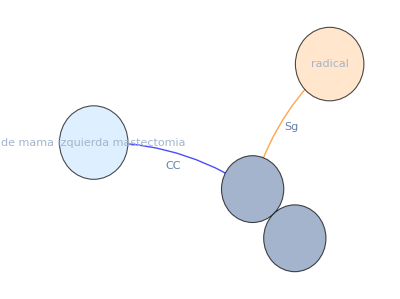

```mathematica
hg=Subgraph[shownGraph,_<->"H:806"]
```

```mathematica
EdgeList[hg]
```

{de mama izquierda mastectomia<->H:806,P:108366<->H:806,radical<->H:806}

```mathematica
GraphSum[pg,hg, Sequence[ PlotTheme -> "Labeled", VertexSize -> 0.2]]
```

-Graphics-

Forma 2

```mathematica
{{"P:108366","P:260615"},{"P:312860","P:95677"}}
```

{{P:108366,P:260615},{P:312860,P:95677}}

```mathematica
ShowRelationGraphs[g1_,g2_]:=
Module[{nodosG1 = VertexList[Subgraph[shownGraph,_<->g1]], nodosG2 = VertexList[Subgraph[shownGraph,_<->g2]],g},
pg1=Subgraph[shownGraph,Table[nodosG1[[i]]<->_,{i,Length[nodosG1]}],Green,Sequence[ PlotTheme -> "Labeled", VertexSize -> 0.2, EdgeStyle -> Blue]];
pg2=Subgraph[shownGraph,Table[nodosG2[[i]]<->_,{i,Length[nodosG2]}],Green,Sequence[ PlotTheme -> "Labeled", VertexSize -> 0.2, EdgeStyle -> Red]];
g= GraphSum[pg1,pg2, Sequence[ PlotTheme -> "Labeled", VertexSize -> 0.5]];
enlacespg1=EdgeList[pg1];
enlacespg2=EdgeList[pg2];
g=HighlightGraph[g,{Table[Style[enlacespg1[[i]],Green],{i,Length[enlacespg1]}]}];
g=HighlightGraph[g,{Table[Style[enlacespg2[[i]],Blue],{i,Length[enlacespg2]}]}]
];
```

```mathematica
ShowRelationGraphs["P:108366","P:260615"]
```

-Graphics-

```mathematica
ShowRelationGraphs["P:312860","P:95677"]
```

-Graphics-

```mathematica
ToLowerCase["hi the girDSADASDAl is over the table"]
```

hi the girdsadasdal is over the table

```mathematica
StringCases["hi  girl    table",WordCharacter..]
```

{hi,girl,table}

```mathematica
Characters["hi  girl    table"]
```

{h,i, , ,g,i,r,l, , , , ,t,a,b,l,e}